Drop of all functions used for project

```mathematica
connectInbox[server_String,username_String]:=(
mail=MailServerConnect["imap."<>server,username];
inbox=mail["INBOX"];
sent=mail["[Gmail]/Sent Mail"];)
connectInbox["gmail.com","23wheels"]
```

```mathematica
mailGet[howmany_Integer?Positive]:=inbox[-howmany;;]
emailStore=mailGet[40];
(*can be any number of emails to store here*)
```

```mathematica
summerizeSearch[outer_Integer,subject_String]:=(
MailSearch[inbox[-outer;;],<|"Subject"->subject|>])
```

```mathematica
topSenders[howmanySenders_Integer?Positive]:=TakeLargest[Counts@Map[#["From"]&,emailStore],howmanySenders];
```

```mathematica
Histogram[topSenders[10]]
```

```mathematica
mostCommon[number_Integer?Positive]:=(
noList=WordList["Stopwords"];
WordCounts[
StringJoin[
Table[
emailStore[[-x]]["Body"],
{x,number}
]]])
```

```mathematica
wordCloud[amount_Integer?Positive]:=(
WordCloud[mostCommon[amount],
WordSelectionFunction->
((StringLength[#]<10)&&
!(noList//MemberQ[#])&&
(!NumberQ[#])&)
])
```

```mathematica
emailWordCloud[number_Integer?Positive]:=(
noList=WordList["Stopwords"];
WordCloud[
WordCounts[
StringJoin[
Table[
inbox[-x]["Body"],
{x,number}
]]],
WordSelectionFunction->
((StringLength[#]<10)&&
!(MemberQ[noList,#])&&
(!NumberQ[#])&)
])
```

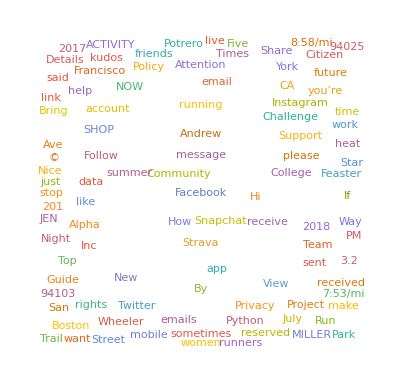

```mathematica
emailWordCloud[25]
```

```mathematica
emailsFromInbox=inbox[-100;;-1];
```

```mathematica
edges=Flatten@Map[
Function[
{message},
fromList=If[StringQ@message["FromAddress"],message["FromAddress"],"weird"];
toList=Select[message["ToAddressList"],StringQ];
ccList=Select[message["ToAddressList"],StringQ];
If[
fromList==="weird",
Nothing,
{
(*DirectedEdge[fromList,#]&/@toList,*)
DirectedEdge[fromList,#]&/@ccList,
Flatten@Outer[UndirectedEdge,toList,ccList]
}
]
],
emailsFromInbox
];
```

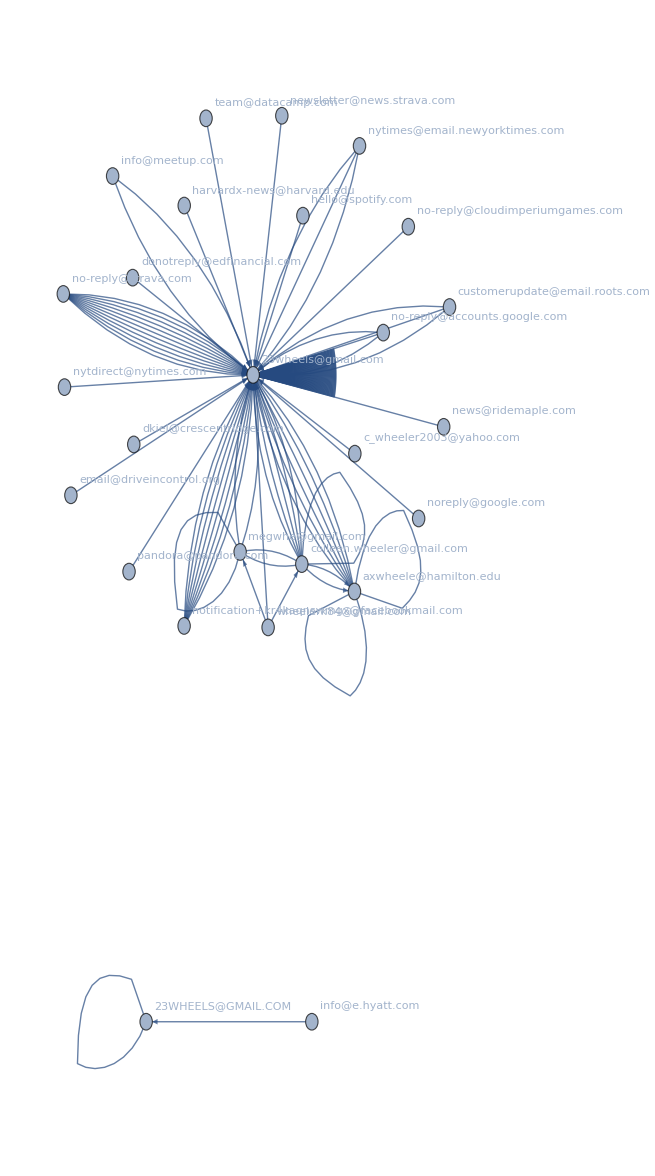

```mathematica
Graph[edges,VertexLabels->"Name"]
```

```mathematica
program[]:=(
serverType=Input["email server","gmail.com"];
loginName=Input["username","23wheels"];
numberWanted=Input["How many previous emails do you want to pull?",15];
start[serverType,loginName]
)
```

```mathematica
start[server_String,username_String,numberofEmails_Integer?Positive]:=(
Clear[mail,inbox,sent,emailStore,noList,edges];
connectInbox[server,username];
(*vars {mail,inbox,sent} all assigned*)
emailsFromInbox=inbox[-numberofEmails;;];
)
```